```mathematica
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\85F11"];
data=Import[#]&/@FileNames["*csv"];
data2=Table[Take[data[[i]],{17,-2}],{i,1,Length[data]}];
```

```mathematica
f[data_]:=Module[{ll,max,min,yaxis1,yaxis2,wcn,ff,gg,loc,kk},
ll=data[[All,2]];
{max,min}=#[ll]&/@{Max,Min};
yaxis1=Take[data[[All,4]],Flatten[{#[ll,min][[1]],#[ll,max][[-1]]}&@Position]];
yaxis2=Take[data[[All,8]],Flatten[{#[ll,min][[1]],#[ll,max][[-1]]}&@Position]];

wcn=(794.76728224*10^-9);


ff[x_]:=Evaluate[Fit[


Flatten[{Table[{o,yaxis1[[o]]},{o,10,200}],Table[{o,yaxis1[[o]]},{o,Length[yaxis1]-200,Length[yaxis1]-10}]},1]

,{1,x},x]];
gg=Table[ff[x],{x,1,Length[yaxis1]}];
loc=Select[FindPeaks[
GaussianFilter[yaxis2,10]
,16,0.00002],1500<#[[1]]<4500&];
kk[x_]:=Evaluate[Fit[{{loc[[1,1]],-0.361},{loc[[-1,1]],-0.361/2}},{1,x},x]];
{-12.531885282826405 wcn Log[yaxis1/gg],GaussianFilter[yaxis1/gg,10],yaxis2,Table[kk[x],{x,1,Length[yaxis1]}]}

]
```

```mathematica
Manipulate[
ListPlot[{GaussianFilter[data2[[i]][[All,8]],10],GaussianFilter[20data2[[i]][[All,4]],10],
Select[FindPeaks[
GaussianFilter[data2[[i]][[All,8]],10]
,16,0.00002],1500<#[[1]]<4500&]},PlotStyle->{Black,{Red,AbsolutePointSize[5]}}]
,{{i,62},1,Length[data2],1}]
```

ListPlot::lpn: {{{1.,0.201046},{2.,0.201084},{3.,0.201113},{4.,0.201146},{5.,0.201159},{6.,0.201208},{7.,0.201262},{8.,0.201299},{9.,0.201332},{10.,0.20138},{11.,0.201431},{12.,0.201464},{13.,0.201495},{14.,0.201546},«23»,{38.,0.200918},{39.,0.200938},{40.,0.200979},{41.,0.201036},{42.,0.201073},{43.,0.201119},{44.,0.201138},{45.,0.201155},{46.,0.201168},{47.,0.201178},{48.,0.201222},{49.,0.201231},{50.,0.201241},«6199»},{«1»},{}} is not a list of numbers or pairs of numbers.

```mathematica
Manipulate[ListPlot[Transpose[f[data2[[i]]][[{4,2}]]],Joined->True,Epilog->Line[{{-2,1},{2,1}}]],{{i,48},1,Length[data2],1}]
```

```mathematica
power
```

{0.5,0.5,0.5,0.5,1,1,1,1,2,2,2,2,3,3,3,3,4,4,4,4,5,5,5,5,6,6,6,6,7,7,7,7,8,8,8,8,9,9,9,9,10,10,10,10,15,15,15,15,20,20,20,20,25,25,25,25,30,30,30,30,35,35,35,35,40,40,40,40,50,50,50,50,60,60,60,60,70,70,70,70,80,80,80,80}

```mathematica
power[[45]]
```

15

```mathematica
final2=ListPlot[{Lev4DoppTestsc[23,15/1000,0.9/1000,1.438*10^6,-361*10^6,0],Lev3DoppTestsc[23,15/1000,0.9/1000,1.438*10^6,-361*10^6,0],Lev3DoppTestsc[23,0/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Bottom}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Darker[Gray],Dashing[.02]},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.8,0.4},{0.4,1.0}}];
Show[final2,ListPlot[Transpose[f[data2[[45]]][[{4,2}]]],Joined->True,PlotStyle->{Thick,Black},Epilog->Line[{{-2,1},{2,1}}]]]
```

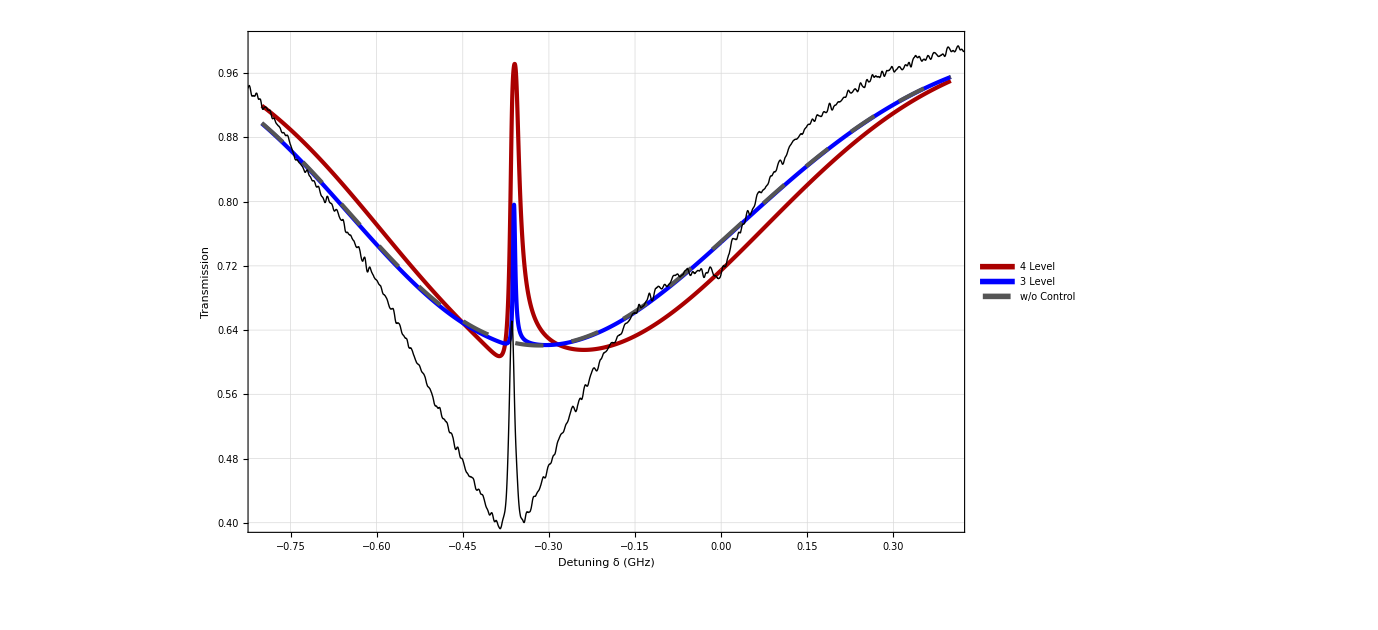

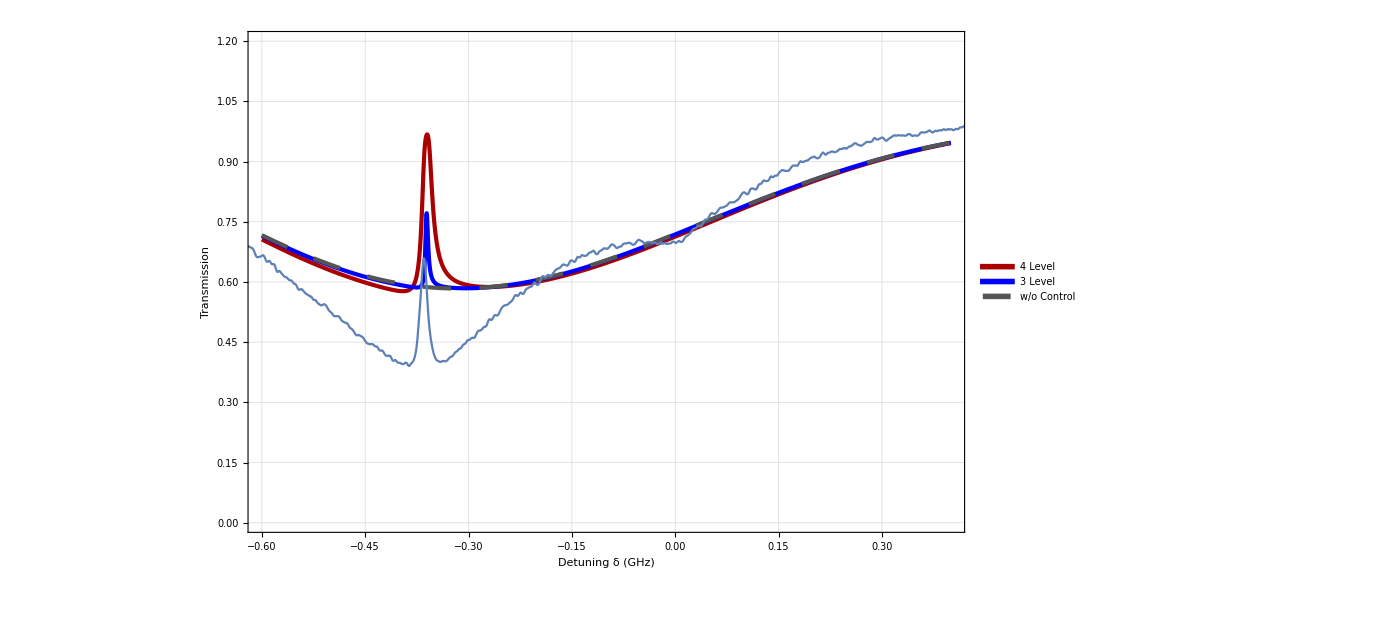

```mathematica
final2=ListPlot[{Lev4DoppTestsc[23,15/1000,0.9/1000,1.438*10^6,-361*10^6,0],Lev3DoppTestsc[23,15/1000,0.9/1000,1.438*10^6,-361*10^6,0],Lev3DoppTestsc[23,0/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Bottom}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Darker[Gray],Dashing[.02]},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.8,0.4},{0.4,1.0}}];
Show[final2,ListPlot[Transpose[f[data2[[45]]][[{4,2}]]],Joined->True,PlotStyle->{Thick,Black},Epilog->Line[{{-2,1},{2,1}}]]]
```

```mathematica
pw={0.5,1,2,3,4,5,6,7,8,9,10,15,20,25,30,35,40,50,60,70,80};power=Flatten[Transpose[{pw,pw,pw,pw}]];
```

```mathematica
Manipulate[ListPlot[Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01-0.361<#[[1]]<0.05-0.361&]],{i,1,Length[data2],1}]
```

```mathematica
pw={0.5,1,2,3,4,5,6,7,8,9,10,15,20,25,30,35,40,50,60,70,80};power=Flatten[Transpose[{pw,pw,pw,pw}]];
EITmax7711=Table[
If[i<14,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.005-0.361<#[[1]]<0.02-0.361&][[All,2]]//Max,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01-0.361<#[[1]]<0.05-0.361&][[All,2]]//Max],{i,1,Length[data],1}];
```

```mathematica
EITmin7711=Table[
If[i<14,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.005-0.361<#[[1]]<0.02-0.361&][[All,2]]//Min,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01-0.361<#[[1]]<0.05-0.361&][[All,2]]//Min],{i,1,Length[data],1}];
```

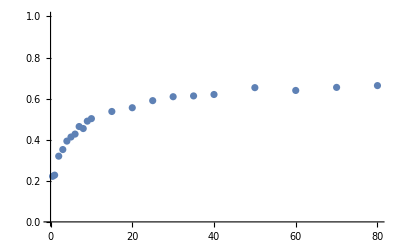

```mathematica
rb8511=ListPlot[{Transpose[{pw,1-Log[Max/@Partition[EITmax7711,4]]/Log[Min/@Partition[EITmin7711,4]]}]},PlotRange->{0,1}]
```

```mathematica
pw={0.5,1,2,3,4,5,6,7,8,9,10,15,20,25,30,35,40,50,60,70,80};power=Flatten[Transpose[{pw,pw,pw,pw}]];
EITmax7711=Table[
If[i<14,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.005-0.361<#[[1]]<0.02-0.361&][[All,2]]//Max,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01-0.361<#[[1]]<0.05-0.361&][[All,2]]//Max],{i,1,Length[data],1}];
```

```mathematica
EITmin7711=Table[
If[i<14,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.005-0.361<#[[1]]<0.02-0.361&][[All,2]]//Min,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01-0.361<#[[1]]<0.05-0.361&][[All,2]]//Min],{i,1,Length[data],1}];
```

{0.510961,0.504105,0.502705,0.503764,0.507851,0.504928,0.495023,0.504948,0.509142,0.510644,0.511593,0.502264,0.511439,0.513055,0.510754,0.509376,0.515543,0.512883,0.513705,0.505429,0.499532,0.515673,0.517006,0.509474,0.505917,0.513395,0.512192,0.504842,0.517417,0.512775,0.519498,0.510371,0.511546,0.504165,0.508848,0.510478,0.517714,0.487217,0.498955,0.503821,0.516184,0.51086,0.512983,0.519697,0.525709,0.519912,0.518711,0.52227,0.525075,0.524514,0.529603,0.530607,0.536859,0.503245,0.541703,0.545056,0.545331,0.548951,0.539514,0.542035,0.540931,0.543888,0.541323,0.5463,0.544114,0.548221,0.549084,0.546605,0.546657,0.554704,0.527205,0.549916,0.557366,0.552458,0.553741,0.551803,0.534179,0.557639,0.558568,0.559706,0.567035,0.564008,0.574331,0.563859}

Nearest::near1: 0.494704 is neither a list of real points nor a valid list of rules.

Nearest::near1: 0.492693 is neither a list of real points nor a valid list of rules.

Nearest::near1: 0.490444 is neither a list of real points nor a valid list of rules.

General::stop: Further output of Nearest::near1 will be suppressed during this calculation.

{{-0.365764,0.494704},{-0.365411,0.492693},{-0.365058,0.490444},{-0.364705,0.488306},{-0.364352,0.486081},{-0.364,0.483529},{-0.363647,0.48137},{-0.363294,0.479171},{-0.362941,0.477341},{-0.362588,0.475617},{-0.362235,0.473796},{-0.361882,0.472394},{-0.361529,0.471169},{-0.361176,0.470332},{-0.360824,0.469751},{-0.360471,0.469358},{-0.360118,0.468942},{-0.359765,0.469224},{-0.359412,0.46993},{-0.359059,0.470932},{-0.358706,0.472133},{-0.358353,0.473995},{-0.358,0.47662},{-0.357648,0.479665},{-0.357295,0.483337},{-0.356942,0.48765},{-0.356589,0.49256},{-0.356236,0.497784},{-0.355883,0.503593},{-0.35553,0.509628},{-0.355177,0.51605},{-0.354825,0.522431},{-0.354472,0.528821},{-0.354119,0.534643},{-0.353766,0.54019},{-0.353413,0.544867},{-0.35306,0.548557},{-0.352707,0.55137},{-0.352354,0.552786},{-0.352001,0.552979},{-0.351649,0.552083},{-0.351296,0.549858},{-0.350943,0.546216},{-0.35059,0.541454},{-0.350237,0.536171},{-0.349884,0.530266},{-0.349531,0.523876},{-0.349178,0.517294},{-0.348826,0.510782},{-0.348473,0.504532},{-0.34812,0.49861},{-0.347767,0.493217},{-0.347414,0.488296},{-0.347061,0.484086},{-0.346708,0.480514},{-0.346355,0.477324},{-0.346002,0.474827},{-0.34565,0.472938},{-0.345297,0.471679},{-0.344944,0.470628},{-0.344591,0.47004},{-0.344238,0.469894},{-0.343885,0.470164},{-0.343532,0.47082},{-0.343179,0.471704},{-0.342826,0.472918},{-0.342474,0.474261},{-0.342121,0.475879},{-0.341768,0.477566},{-0.341415,0.479659},{-0.341062,0.48167}}

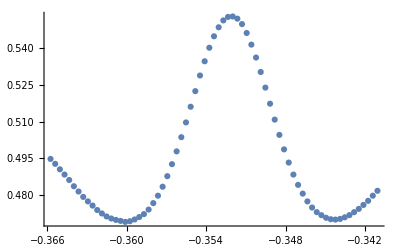

```mathematica
xBest=halfv[[1]];
{#[[1]],First@Nearest[#[[2]],xBest]}&/@Select[Transpose[f[data2[[1]]][[{4,2}]]],-0.005-0.361<#[[1]]<0.02-0.361&]
ListPlot[%]
```

```mathematica
halfv=EITmin7711+(EITmax7711-EITmin7711)/2
```

```mathematica
Manipulate[
Which[i<=14,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.004-0.361<#[[1]]<0.018-0.361&];,
72≥ i>14,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.015-0.361<#[[1]]<0.03-0.361&];,
72<i,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.03-0.361<#[[1]]<0.05-0.361&];
];
Nearest[ddd[[All,2]],halfv[[i]],4];
pos=Position[ddd[[All,2]],#]&/@Nearest[ddd[[All,2]],halfv[[1]],6];
ddd1=ddd[[Sort[Flatten[pos]]]];
f1=Evaluate[Fit[ddd1[[{1,2}]],{1,x},x]];
f2=Evaluate[Fit[ddd1[[{-1,-2}]],{1,x},x]];
Show[ListPlot[{ddd,ddd1},PlotStyle->{Black,{Blue,AbsolutePointSize[8]}},Epilog->Line[{{-1,halfv[[1]]},{1,halfv[[1]]}}]],Plot[{f1,f2},{x,-0.375,-0.30},PlotRange->{0,1},PlotStyle->{{Red,Dashed},{Red,Dashed}}]]
,{i,1,Length[data2],1}]
Abs[Solve[f1==halfv[[1]],x][[1,1,2]]-Solve[f2==halfv[[1]],x][[1,1,2]]]*10^3(*in MHz*)
```

27.6801

Part::partd: Part specification halfv⟦69⟧ is longer than depth of object.

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair halfv⟦69⟧ and 0.843107.

Part::partd: Part specification halfv⟦1⟧ is longer than depth of object.

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair halfv⟦1⟧ and 0.843107.

Nearest::near1: {{}} is neither a list of real points nor a valid list of rules.

Nearest::near1: {} is neither a list of real points nor a valid list of rules.

Part::pkspec1: The expression Nearest[{},{},{{}}] cannot be used as a part specification.

Fit::fitd: First argument {{-0.375718,0.843107},{-0.375302,0.843165},{-0.374885,0.843076},{-0.374469,0.84293},{-0.374052,0.842749},{-0.373636,0.842678},{-0.373219,0.84268},{-0.372802,0.842904},{-0.372386,0.843079},«33»,{-0.358224,0.84575},{-0.357807,0.845581},{-0.357391,0.845858},{-0.356974,0.846087},{-0.356557,0.846686},{-0.356141,0.847145},{-0.355724,0.847419},{-0.355308,0.847973},«58»}⟦Nearest[«1»]⟧ in Fit is not a list or a rectangular array.

Part::pkspec1: The expression Nearest[{},{},{{}}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Fit::fitd: First argument {{-0.375718,0.843107},{-0.375302,0.843165},{-0.374885,0.843076},{-0.374469,0.84293},{-0.374052,0.842749},{-0.373636,0.842678},{-0.373219,0.84268},{-0.372802,0.842904},{-0.372386,0.843079},«33»,{-0.358224,0.84575},{-0.357807,0.845581},{-0.357391,0.845858},{-0.356974,0.846087},{-0.356557,0.846686},{-0.356141,0.847145},{-0.355724,0.847419},{-0.355308,0.847973},«58»}⟦Nearest[«1»]⟧ in Fit is not a list or a rectangular array.

General::stop: Further output of Fit::fitd will be suppressed during this calculation.

Part::partd: Part specification halfv⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

General::ivar: -0.374998 is not a valid variable.

General::ivar: -0.373468 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

```mathematica
width8511=Table[
Which[i<=14,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.004-0.361<#[[1]]<0.018-0.361&];,
72≥ i>14,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.015-0.361<#[[1]]<0.03-0.361&];,
72<i,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.03-0.361<#[[1]]<0.05-0.361&];
];

Nearest[ddd[[All,2]],halfv[[i]],4];
pos=Position[ddd[[All,2]],#]&/@Nearest[ddd[[All,2]],halfv[[1]],6];
ddd1=ddd[[Sort[Flatten[pos]]]];
f1=Evaluate[Fit[ddd1[[{1,2}]],{1,x},x]];
f2=Evaluate[Fit[ddd1[[{-1,-2}]],{1,x},x]];
{power[[i]],Abs[Solve[f1==halfv[[1]],x][[1,1,2]]-Solve[f2==halfv[[1]],x][[1,1,2]]]*10^3}
,{i,1,Length[data2],1}]
(*in MHz*)
```

{{0.5,6.61679},{0.5,4.96064},{0.5,5.87608},{0.5,5.42528},{1,6.4781},{1,6.65319},{1,3.29395},{1,5.79629},{2,7.31526},{2,8.8695},{2,8.76987},{2,6.67881},{3,9.01657},{3,8.55189},{3,7.46948},{3,8.20004},{4,8.40642},{4,9.37722},{4,8.55355},{4,7.9258},{5,6.08853},{5,9.61066},{5,9.12859},{5,8.44129},{6,7.65894},{6,8.55851},{6,8.9792},{6,7.17764},{7,9.241},{7,8.41711},{7,12.4285},{7,7.87359},{8,7.64605},{8,7.9792},{8,8.42443},{8,8.34407},{9,10.0006},{9,4.70844},{9,7.19519},{9,7.83246},{10,9.10029},{10,9.71421},{10,9.0722},{10,10.5546},{15,11.9346},{15,10.9465},{15,11.6132},{15,12.7849},{20,13.0923},{20,12.4679},{20,13.7639},{20,12.4703},{25,15.9828},{25,14.9845},{25,16.5666},{25,17.3485},{30,18.7752},{30,21.3014},{30,19.9796},{30,18.8575},{35,19.7244},{35,19.4232},{35,20.1687},{35,21.5911},{40,22.6721},{40,24.3325},{40,23.4241},{40,23.6429},{50,37.2622},{50,27.2235},{50,22.3439},{50,27.6801},{60,29.4293},{60,27.5153},{60,28.504},{60,23.2266},{70,27.7413},{70,31.0584},{70,30.3984},{70,32.9254},{80,36.3428},{80,36.3189},{80,39.7147},{80,37.526}}

```mathematica
39,69
```

```mathematica
Max/@
```

```mathematica
rb85w11={{0.5,6.61678768099666},{0.5,4.960640766355551},{0.5,5.876078830758469},{0.5,5.425279602919497},{1,6.47809642577557},{1,6.6531906389991065},{1,3.293946754409194},{1,5.796291730324032},{2,7.3152597122144725},{2,8.869502652332939},{2,8.769869721931334},{2,6.678812940710543},{3,9.016567174921441},{3,8.551890678616891},{3,7.469482742967881},{3,8.200038774431373},{4,8.406419016120825},{4,9.377220949458753},{4,8.553553757709443},{4,7.925803526791563},{5,6.088534592967321},{5,9.610659389341137},{5,9.128590945008286},{5,8.441293184791586},{6,7.658936729801502},{6,8.558509532716418},{6,8.979200867488935},{6,7.1776382478851986},{7,9.241001123342585},{7,8.417113593190473},{7,12.428461236382526},{7,7.87358854014647},{8,7.646047130097033},{8,7.979199204343979},{8,8.424431675381427},{8,8.344074126238276},{9,10.000571072340703},{9,4.708442782433209},{9,7.195192821197793},{9,7.832460457748436},{10,9.100293931857074},{10,9.71421140454104},{10,9.072195271100759},{10,10.554624045464367},{15,11.934560989647125},{15,10.9465261402108},{15,11.613170326125854},{15,12.784880915979457},{20,13.092280900274256},{20,12.467931686045597},{20,13.7638843410543},{20,12.470323751947621},{25,15.982765247618769},{25,14.984468375097148},{25,16.566589155274038},{25,17.34853841279338},{30,18.775184313015004},{30,21.30144877469592},{30,19.979604743668723},{30,18.857477825701185},{35,19.724393715842947},{35,19.423179342287934},{35,20.168681449156402},{35,21.591138436804826},{40,22.67213717570604},{40,24.332535572442303},{40,23.424086476211635},{40,23.642945202246967},{50,37.262174406153036},{50,27.223453590528745},{50,22.343880667935522},{50,27.680114657392895},{60,29.429286684957646},{60,27.515342247079687},{60,28.503970253907664},{60,23.22660469180332},{70,27.74131933401891},{70,31.058401791115188},{70,30.398385946253768},{70,32.925411300428806},{80,36.34283527515198},{80,36.31891518137992},{80,39.714706110446144},{80,37.52602221539697}}
```

{{0.5,6.61679},{0.5,4.96064},{0.5,5.87608},{0.5,5.42528},{1,6.4781},{1,6.65319},{1,3.29395},{1,5.79629},{2,7.31526},{2,8.8695},{2,8.76987},{2,6.67881},{3,9.01657},{3,8.55189},{3,7.46948},{3,8.20004},{4,8.40642},{4,9.37722},{4,8.55355},{4,7.9258},{5,6.08853},{5,9.61066},{5,9.12859},{5,8.44129},{6,7.65894},{6,8.55851},{6,8.9792},{6,7.17764},{7,9.241},{7,8.41711},{7,12.4285},{7,7.87359},{8,7.64605},{8,7.9792},{8,8.42443},{8,8.34407},{9,10.0006},{9,4.70844},{9,7.19519},{9,7.83246},{10,9.10029},{10,9.71421},{10,9.0722},{10,10.5546},{15,11.9346},{15,10.9465},{15,11.6132},{15,12.7849},{20,13.0923},{20,12.4679},{20,13.7639},{20,12.4703},{25,15.9828},{25,14.9845},{25,16.5666},{25,17.3485},{30,18.7752},{30,21.3014},{30,19.9796},{30,18.8575},{35,19.7244},{35,19.4232},{35,20.1687},{35,21.5911},{40,22.6721},{40,24.3325},{40,23.4241},{40,23.6429},{50,37.2622},{50,27.2235},{50,22.3439},{50,27.6801},{60,29.4293},{60,27.5153},{60,28.504},{60,23.2266},{70,27.7413},{70,31.0584},{70,30.3984},{70,32.9254},{80,36.3428},{80,36.3189},{80,39.7147},{80,37.526}}

{{0.5,6.61679},{0.5,4.96064},{0.5,5.87608},{0.5,5.42528},{1,6.4781},{1,6.65319},{1,3.29395},{1,5.79629},{2,7.31526},{2,8.8695},{2,8.76987},{2,6.67881},{3,9.01657},{3,8.55189},{3,7.46948},{3,8.20004},{4,8.40642},{4,9.37722},{4,8.55355},{4,7.9258},{5,6.08853},{5,9.61066},{5,9.12859},{5,8.44129},{6,7.65894},{6,8.55851},{6,8.9792},{6,7.17764},{7,9.241},{7,8.41711},{7,12.4285},{7,7.87359},{8,7.64605},{8,7.9792},{8,8.42443},{8,8.34407},{9,10.0006},{9,4.70844},{9,7.19519},{9,7.83246},{10,9.10029},{10,9.71421},{10,9.0722},{10,10.5546},{15,11.9346},{15,10.9465},{15,11.6132},{15,12.7849},{20,13.0923},{20,12.4679},{20,13.7639},{20,12.4703},{25,15.9828},{25,14.9845},{25,16.5666},{25,17.3485},{30,18.7752},{30,21.3014},{30,19.9796},{30,18.8575},{35,19.7244},{35,19.4232},{35,20.1687},{35,21.5911},{40,22.6721},{40,24.3325},{40,23.4241},{40,23.6429},{50,37.2622},{50,27.2235},{50,22.3439},{50,27.6801},{60,29.4293},{60,27.5153},{60,28.504},{60,23.2266},{70,27.7413},{70,31.0584},{70,30.3984},{70,32.9254},{80,36.3428}}

```mathematica
Transpose[{pw,Mean/@Partition[width8511[[All,2]],4]}]
```

{{0.5,5.7197},{1,5.55538},{2,7.90836},{3,8.30949},{4,8.56575},{5,8.31727},{6,8.09357},{7,9.49004},{8,8.09844},{9,7.43417},{10,9.61033},{15,11.8198},{20,12.9486},{25,16.2206},{30,19.7284},{35,20.2268},{40,23.5179},{50,28.6274},{60,27.1688},{70,30.5309},{80,37.4756}}

{6.61679,6.65319,8.8695,9.01657,9.37722,9.61066,8.9792,12.4285,8.42443,10.0006,10.5546,15,20,25,30,35,40,50,60,70,431.786}

```mathematica
width8511[[39]]
```

{9,7.19519}

```mathematica
Transpose[{pw,width8511}]
```

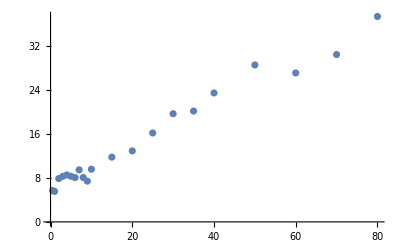

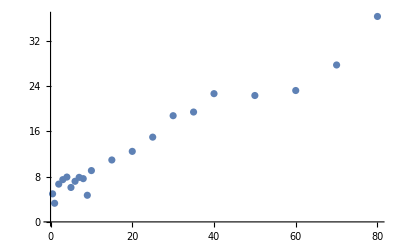

```mathematica
ListPlot[Transpose[{pw,Mean/@Partition[width8511[[All,2]],4]}]]
ListPlot[Transpose[{pw,Min/@Partition[width8511[[All,2]],4]}]]
```

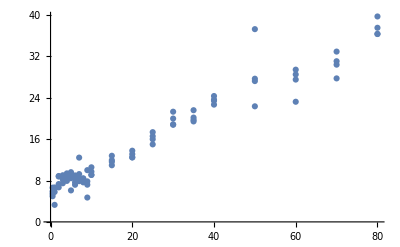

```mathematica
ListPlot[width8511]
```

```mathematica
f1[1]
```

(6.98007+18.1994 x)[1]

```mathematica
Plot[{f1[x],f2[x]},{x,-0.365,-0.345},PlotRange->{0,1}]
```

-Graphics-

{30,31,48,49}

```mathematica
Position[ddd,Nearest[ddd[[All,2]],halfv[[1]],4]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Nearest::near1: Symbol[] is neither a list of real points nor a valid list of rules.

{}

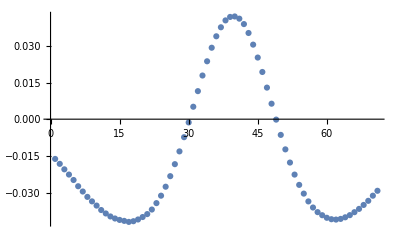

```mathematica
ListPlot[Select[Transpose[f[data2[[1]]][[{4,2}]]],-0.005-0.361<#[[1]]<0.02-0.361&][[All,2]]-halfv[[1]]]
```

```mathematica
FindRoot[Evaluate[Interpolation[][x]]==halfv[[1]],x]
```

FindRoot::fdss: Search specification x should be a list with 1 to 5 elements.

FindRoot[Evaluate[Interpolation[Select[Transpose[f[data2⟦1⟧]⟦{4,2}⟧],-0.005-0.361<#1⟦1⟧<0.02-0.361&]][x]]==halfv⟦1⟧,x]

```mathematica
ListPlot[Select[Transpose[f[data2[[1]]][[{4,2}]]],-0.005-0.361<#[[1]]<0.02-0.361&]]
```

-Graphics-